```mathematica
单线圈电力线的分布——折线法
```

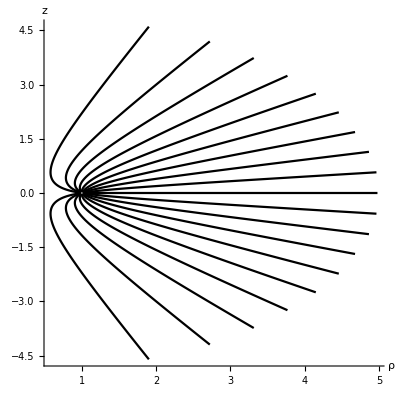

```mathematica
R=1;a=R^2+z^2+ρ^2;b=2ρ*R;
V[ρ_,z_]:=(2 EllipticK[(2 b)/(-a+b)])/(√(a-b))+(2 EllipticK[(2 b)/(a+b)])/(√(a+b));
field=-D[V[ρ,z],ρ]-ⅈ*D[V[ρ,z],z];
step=0.03;r1=0.02;r2=5;forceline={};
Do[
θ=ϕ;single={p1={1,0}+r1 {Cos[ϕ],Sin[ϕ]}};
Label[ss];p=Last[single];
p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];
If[(Norm[p1-p]>r1)∧(Norm[p]<r2),
AppendTo[single,p];Goto[ss]];
AppendTo[forceline,single],
{ϕ,-π+π/10,π-π/10,π/10}]
Show[
Graphics[{Thickness[0.004],Line/@forceline}],
Axes->True,AxesStyle->Thickness[0.003],
AspectRatio->1,AxesLabel->{"ρ","z"},
AxesOrigin->{0,0},BaseStyle->{FontSize->13}]
Clear[V]
```